```mathematica
Тестовая функция
u[x_]:=Sin[x/5] x^2 Log[x]
D[u[x],x]
u[1]
```

функция Тестовая

1/5 x^2 Cos[x/5] Log[x]+x Sin[x/5]+2 x Log[x] Sin[x/5]

0

```mathematica
NDSolveValue[{y'[x]==1/5 y[x]Cot[x/5]+2 y[x]/x+x Sin[x/5],y[1]==0},y[x],{x,1,5}]
```

InterpolatingFunction[…][x]

```mathematica
DSolve[{y'[x]==1/5 y[x]Cot[x/5]+2 y[x]/x+x Sin[x/5]},y[x],x]
```

{{y[x]→x^2 C[1] Sin[x/5]+x^2 Log[x] Sin[x/5]}}

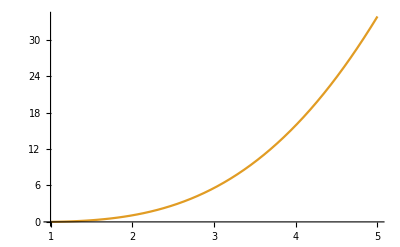

```mathematica
Plot[{%,u[x]},{x,1,5}]
```

Количество точек (кроме последней): 32

Сеточное решение:

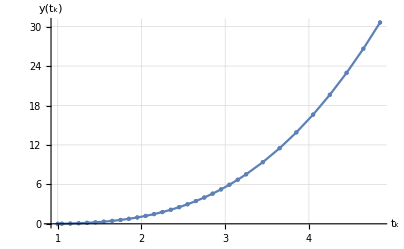

Поточечная величина нормы абслютного отклонения:

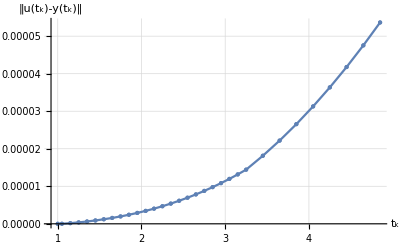

Поточечная оценка локальной ошибки ϵ:

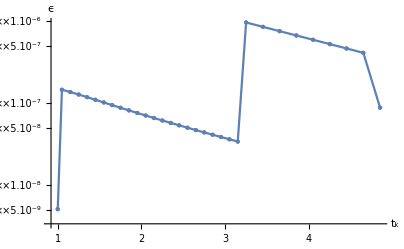

Величина шага τ:

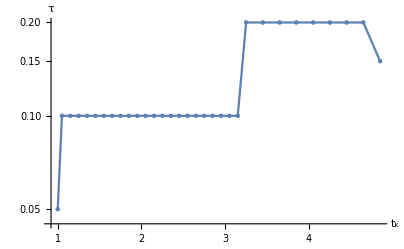

```mathematica
RK4RungeData=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\RK4auto.txt","Table"];
Block[{t=RK4RungeData[[;;,1]],err=RK4RungeData[[;;,-3]],ϵ=RK4RungeData[[;;,-2]],τ=RK4RungeData[[;;,-1]],y=RK4RungeData[[;;,2;;-4]],data},
Print["Количество точек (кроме последней): ", Length@t];
Print["Сеточное решение:"];
Print@Switch[Length@y[[1]],
1,data=Transpose[{t,Flatten@y}];ListLinePlot[data(*{data,Table[{t[[i]],u[t[[i]]]},{i,1,Length@t}]}*),Mesh->Full,MeshStyle->Directive[PointSize[Medium]],LabelStyle->{FontSize->14(*,FontFamily->"Times New Roman"*)}, Ticks->Automatic,InterpolationOrder->1,GridLines->Automatic,AxesLabel->{"t_k","y(t_k)"}],
2,data=Flatten[Thread/@Transpose@{t,y},1];ListLinePlot3D[data]];
Print["Поточечная величина нормы абслютного отклонения:"];
Print@ListLinePlot[Transpose@{t,err},GridLines->Automatic,AxesLabel->{"t_k","‖u(t_k)-y(t_k)‖"},Mesh->Full,MeshStyle->Directive[PointSize[Medium]],LabelStyle->{FontSize->14}];
Print["Поточечная оценка локальной ошибки ϵ:"];
Print@ListLinePlot[Transpose@{t,ϵ},ScalingFunctions->"Log10",GridLines->Automatic,AxesLabel->{"t_k","ϵ"},Mesh->Full,MeshStyle->Directive[PointSize[Medium]],LabelStyle->{FontSize->14}];
Print["Величина шага τ:"];
Print@ListLinePlot[Transpose@{t,τ},ScalingFunctions->"Log10",GridLines->Automatic,AxesLabel->{"t_k","τ"},Mesh->Full,MeshStyle->Directive[PointSize[Medium]],LabelStyle->{FontSize->14}];
]
```